```mathematica
(* Run this set of commands to check if the Lsep, Rmin, Smin values are correct *)
(* R. Sheehan November 2018 *)

(* Seek out all the Mathematica Modules you wrote for PhD thesis Numerical Analysis and put them on GitHub *)
(* Also the scattering matrix analysis for 1D waveguides is located in your PhD thesis folder *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Robert\Programming\C++\AWG_Design\AWG_Design\AWG_Design

## Module Definitions

```mathematica
MinY[ll_]:=
Module[{tmp,tmpy},
(* Returns the smallest vertical ordinate in a list of the form {{x1, y1},{x2, y2},{x3, y3},.....} *)
tmp=Table[ll⟦i,2⟧,{i,1,Length[ll]}];
tmpy=Min[tmp];
Return[tmpy];
]
```

```mathematica
MaxY[ll_]:=
Module[{tmp,tmpy},
(* Returns the largest vertical ordinate in a list of the form {{x1, y1},{x2, y2},{x3, y3},.....} *)
tmp=Table[ll⟦i,2⟧,{i,1,Length[ll]}];
tmpy=Max[tmp];
Return[tmpy];
]
```

```mathematica
InfNorm[x_]:=Module[
{vmax,indx,t1,res},
(* Return the infinity norm of the vector x and its associated index *)
(* This returns the inf norm with its sign intact *)
(* R. Sheehan 4 - 3 - 2012 *)
vmax=0;
Do[
t1=x⟦i⟧;
If[Abs[t1]>Abs[vmax],vmax=t1;indx=i];
,{i,1,Length[x]}
];
res={vmax,indx};
Return[N[vmax]]
]
```

```mathematica
MinWithIndx[ll_]:=Module[
{vmin,pmin, indxmin,t1},
(* return the min ordinate value in a list of the form {{x1, y1},{x2, y2},{x3, y3},.....} *)
(* Print the absissa for which minimum occurs and its indx *)
(* R. Sheehan 24 - 6 - 2019 *)
vmin=0.0; 
Do[
t1=N[ll⟦i,2⟧];
If[t1<vmin,vmin=t1;pmin=ll⟦i,1⟧;indxmin=i;];
,{i,1,Length[ll]}];
Print["Min. pos: ",pmin,", Min. val: ",vmin];
Return[{indxmin, pmin, vmin}]
]
```

```mathematica
MaxWithIndx[ll_]:=Module[
{vmax,pmax, indxmax,t1},
(* return the max ordinate value in a list of the form {{x1, y1},{x2, y2},{x3, y3},.....} *)
(* Print the absissa for which maximum occurs and its indx *)
(* R. Sheehan 24 - 6 - 2019 *)
vmax=0.0; 
Do[
t1=N[ll⟦i,2⟧];
If[t1<vmax,vmax=t1;pmax=ll⟦i,1⟧;indxmax=i;];
,{i,1,Length[ll]}];
Print["Min. pos: ",pmax,", Min. val: ",vmax];
Return[{indxmax, pmax, vmax}]
]
```

```mathematica
NormaliseList[ll_]:=
Module[{tmp,tmp1,max,min,normconst},
(* Normalise a data set to unity *)
tmp=ll;
max=Abs[MaxY[tmp]];
min=Abs[MinY[tmp]];
normconst=Max[max,min];
tmp1=Table[{tmp⟦i,1⟧,tmp⟦i,2⟧/normconst},{i,1,Length[tmp]}];
Return[tmp1];
]
```

```mathematica
NormaliseData[ll_,n_]:=
Module[{llnew},
(* Normalise a matrix of data to unity  *)
llnew=Table[0,{n}];
Table[llnew⟦i⟧=NormaliseList[ll⟦i⟧],{i,1,n}];
Return[llnew];
]
```

```mathematica
ReadTwoCol[file_]:=
Module[{ll},
(* Read in data from a two-column file and return the data as a list of data points in the form {{x1, y1},{x2, y2},{x3, y3},.....} *)
ll=Partition[ReadList[file,Real,RecordSeparators->","],2];
Return[ll];
]
```

```mathematica
ReadMultiCol[file_,n_]:=
Module[{ll,l1},
(* Read in data from an n-column file and return the data as a list of data points in the form {{},{},{},......} *)
l1=ReadList[file,Real,RecordSeparators->" "];
ll=Transpose[Partition[l1,n]];
Return[ll];
]
```

```mathematica
FormatMultiCol[ll_]:=
Module[{tmptab},
(* Formats the data from a multi-column file in the form of lists that can be plotted, input to this function must be the output from ReadMultiCol, assumes that each list is of the same length, 
a not unreasonable assumption *)
tmptab=Table[{ll⟦1,j⟧,ll⟦i+1,j⟧},{i,1,Length[ll]-1},{j,1,Length[ll⟦1⟧]}];
Return[tmptab];
]
```

```mathematica
ReadFormatMultiCol[file_,n_]:=
Module[{l1,l2},
(* Read the data from a multi column and format the data so that it can be plotted, i.e. combine two steps into one *)
l1=ReadMultiCol[file,n];
l2=FormatMultiCol[l1];
Return[l2];
]
```

```mathematica
PlotTwoColList[ll_,title_]:=
Module[{xmin=ll⟦1,1⟧,xmax=ll⟦Length[ll],1⟧,ymin,ymax,δ},
(* Plot a data set, of the form {{x1, y1},{x2, y2},{x3, y3},.....}, within the range of the data *)
δ=0.05;
ymin=MinY[ll];
If[ymin≥0,ymin=0];
ymax=MaxY[ll];
Return[
ListPlot[ll,
PlotRange->{{xmin-δ,xmax+δ},{ymin-δ,ymax+δ}},
PlotLabel->title,PlotMarkers->None,
PlotStyle->{Thick,Red},
AxesStyle->Thick,Joined->True,
LabelStyle->Directive[Bold,Medium]
]
];
]
```

## Length of all arrayed waveguides given Rmin, Smin and θmin - Type I Layout

```mathematica
T1=-0.268184; (* Angle that first array waveguide makes with horizontal *)
dT = Abs[0.268184 - 0.256524]; (* angle separation between array waveguides on input/output aperture *)
Lf=857.62; (* length of slab region *)
Sn=20; (* min. length of array straight section *)
Rn=2000;(* smallest array bend radius *)
dL=138.63; (* Array optical path-length difference *)
nn=47; (* Number of arrayed Waveguides *)
```

```mathematica
Sep[Rn_,Ta_,Ti_,Lf_,Sn_]:=2(Rn Sin[Ti+Ta]+(Lf+Sn)Cos[Ti+Ta]); (* separation between slab regions *)
```

```mathematica
Ltj[Sn_,Rn_,Ti_,Ta_,dL_,j_]:=Sn+Rn (Ti+Ta)+(j-1)dL/2;(* Known length of jth arm of arrayed waveguide *)
```

```mathematica
(* Test to see if the numerical and analytical formulae give the same answer for slab separation *)
data=FindMaximum[Sep[Rn,x,T1,Lf,Sn],{x,(70π)/180}];(* Find angle Ta which maximises slab separation *)
Ta=ArcTan[Rn/(Lf+Sn)]-T1; (* Exact value of angle Ta which maximises slab separation *)
Ls=Sep[Rn,Ta,T1,Lf,Sn]; (* Computed slab separation *)

Print["Numerical Ta-deg = ",(180data⟦2,-1,-1⟧)/π,", Ta-rad = ",data⟦2,-1,-1⟧,", Analytical θ^a = θ_n^max - θ_i^s = ",Ta," rad"]
Print["Numerical 1/2Ls = ",data⟦1⟧/2," um, Analytical 1/2Ls = ",Ls/2," um"]
Print["Min Length: Sn + Rn (T1 + Ta) = ",Sn+Rn (T1+Ta)]
```

Numerical Ta-deg = 81.6735, Ta-rad = 1.42547, Analytical θ^a = θ_n^max - θ_i^s = 1.42547 rad

Numerical 1/2Ls = 2184.08 um, Analytical 1/2Ls = 2184.08 um

Min Length: Sn + Rn (T1 + Ta) = 2334.57

```mathematica
alllengths = Table[{Ta+T1+(j-1)dT,Ltj[Sn,Rn,T1,Ta,dL,j]},{j,1,nn,1}]; (* Compute all known lengths of the AWG arms *)
```

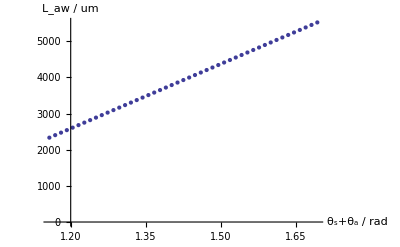

```mathematica
ListPlot[alllengths,AxesLabel->{"θ_s+θ_a / rad","L_aw / um"}]
```

```mathematica
(* Test to see if one of the constraints is satisfied *)
(*j=1;
While[j≤ nn,
LHS = 2(Lf+alllengths⟦j,2⟧)Cos[Ta+T1+(j-1)dT];
If[LHS>Ls,Print["j = ",j,", LHS = ",LHS,", Ls = ",Ls,", LHS > Ls ⇒ Rj < 0"];Break[];];
j++
]*)
```

```mathematica
allradii=Table[{Ta+T1+(j-1)dT,(Ls/2-(Lf+alllengths⟦j,2⟧)Cos[Ta+T1+(j-1)dT])/(Sin[Ta+T1+(j-1)dT]-(Ta+T1+(j-1)dT)Cos[Ta+T1+(j-1)dT])},{j,1,nn,1}];(* Compute all radius values, must have each one positive *)
```

```mathematica
(* Is it possible to determine the extrema of this function? *)
```

```mathematica
(* Check to see that all Subscript[R, j] are positive *)
j=1;
While[j≤ nn,
If[allradii⟦j,2⟧<0.0,Print["j = ",j,": Rj < 0"];Break[];];
j++
]
```

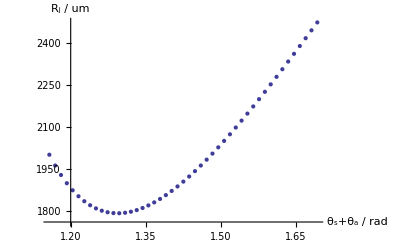

```mathematica
ListPlot[allradii,AxesLabel->{"θ_s+θ_a / rad","R_j / um"}]
```

```mathematica
allss=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-allradii⟦j,2⟧(Ta+T1+(j-1)dT)},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

```mathematica
(* Check to see that all Subscript[S, j] are positive *)
j=1;
While[j≤ nn,
If[allss⟦j,2⟧<0.0,Print["j = ",j,": Rj < 0"];Break[];];
j++
]
```

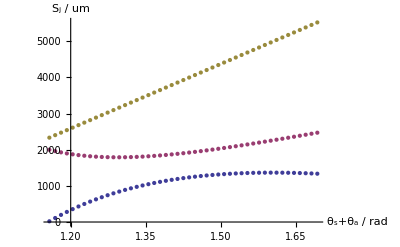

```mathematica
ListPlot[{allss,allradii,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}](* Plot Subscript[S, j], Subscript[R, j] and Subscript[L, j] together *)
```

```mathematica
alltotalL=Table[{Ta+T1+(j-1)dT,(allss⟦j,2⟧+allradii⟦j,2⟧(Ta+T1+(j-1)dT))},{j,1,nn,1}];(* Compute total length using Subscript[S, j] and Subscript[R, j] *)
```

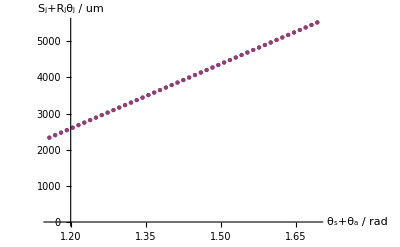

```mathematica
ListPlot[{alltotalL,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j+R_jθ_j / um"}](* Plot lengths computed by the two methods *)
```

```mathematica
alldiffl=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-(allss⟦j,2⟧+allradii⟦j,2⟧(Ta+T1+(j-1)dT))},{j,1,nn,1}];
```

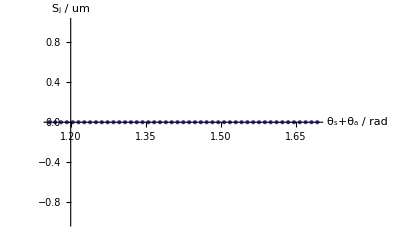

```mathematica
ListPlot[alldiffl,AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]
```

```mathematica
allconstraints=Table[{Ta+T1+(j-1)dT,((Lf+allss⟦j,2⟧)Cos[Ta+T1+(j-1)dT]+allradii⟦j,2⟧Sin[Ta+T1+(j-1)dT])-Ls/2},{j,1,nn,1}];
```

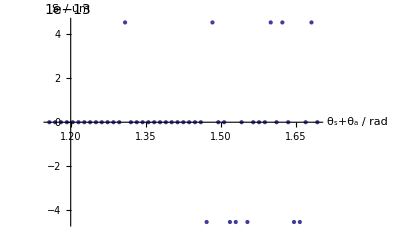

```mathematica
ListPlot[allconstraints,AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]
```

## Analysis of Variation of θ_a

```mathematica
(* Had a look at the max angle condition for choosing Subscript[θ, a]. It turns out that for certain values of Subscript[θ, a] you will get values of Subscript[R, j]<0. This is not acceptable. The problem lies with the arbitrary choise of Sn. It turns out that choosing a value of Subscript[θ, a] is better and computing Sn accordingly is better than letting Sn be arbitrary input. Depending on the choice different formulae arise for computing Sn. Different strategies then come about depending on other constraints. For example, it may be the case the letting Subscript[θ, a]+Subscript[θ, n]=π/4 gives an AWG layout that works, but the min vlaue of Subscript[R, j] in this case may less than 100 um which is not great for bend losses. You can then iterate through different values of Subscript[S, n] to get acceptable value of min Subscript[R, j]. Alternatively you can choose Subscript[θ, a]+Subscript[θ, n] = π/6, though this may not work in all cases either. I've found that the choice of Subscript[θ, a]=π/2 usually works and gives a fairly squared off AWG. What you have to remember is that other parameters such as channel spacing and FSR also affect the layout geometry. Footprint is inversely proportional to channel spacing. No. of channels is directly proportional to FSR so you just have to be careful and make ajustments as necessary.   *)
(* R. Sheehan 9 - 7 - 2019 *)
```

## Length of all arrayed waveguides given Rmin, Smin and θmin - Type II Layout

```mathematica
T1=-0.268184; (* Angle that first array waveguide makes with horizontal *)
dT = Abs[0.268184 - 0.256524]; (* angle separation between array waveguides on input/output aperture *)
Lf=857.62; (* length of slab region *)
Sn=100; (* min. length of array straight section *)
Qn=100; (* min. length of middle straight section *)
Rn=900;(* smallest array bend radius *)
dL=138.63; (* Array optical path-length difference *)
nn=47; (* Number of arrayed Waveguides *)
```

```mathematica
angles=Table[Ta+T1+(j-1)dT,{j,1,nn,1}];
```

```mathematica
SepII[Rn_,Ta_,Ti_,Lf_,Sn_,Qn_]:=2(Rn Sin[Ti+Ta]+(Lf+Sn)Cos[Ti+Ta]+Qn); (* separation between slab regions *)
```

```mathematica
LtjII[Qn_,Sn_,Rn_,Ti_,Ta_,dL_,j_]:=Sn+Qn+Rn (Ti+Ta)+(j-1)dL/2;(* Known length of jth arm of arrayed waveguide *)
```

```mathematica
(* Test to see if the numerical and analytical formulae give the same answer for slab separation *)
data=FindMaximum[SepII[Rn,x,T1,Lf,Sn,Qn],{x,(70π)/180}];(* Find angle Ta which maximises slab separation *)
Ta=ArcTan[Rn/(Lf+Sn)]-T1; (* Exact value of angle Ta which maximises slab separation *)
Ls=SepII[Rn,Ta,T1,Lf,Sn,Qn]; (* Computed slab separation *)

Print["Numerical Ta-deg = ",(180data⟦2,-1,-1⟧)/π,", Ta-rad = ",data⟦2,-1,-1⟧,", Analytical θ^a = θ_n^max - θ_i^s = ",Ta," rad"]
Print["Numerical 1/2Ls = ",data⟦1⟧/2," um, Analytical 1/2Ls = ",Ls/2," um"]
Print["Min Length: Sn + Rn (T1 + Ta) = ",Sn+Qn+Rn (T1+Ta)]
```

Numerical Ta-deg = 58.5892, Ta-rad = 1.02257, Analytical θ^a = θ_n^max - θ_i^s = 1.02257 rad

Numerical 1/2Ls = 1414.17 um, Analytical 1/2Ls = 1414.17 um

Min Length: Sn + Rn (T1 + Ta) = 878.951

```mathematica
alllengths = Table[{angles⟦j⟧,LtjII[Qn,Sn,Rn,T1,Ta,dL,j]},{j,1,nn,1}]; (* Compute all known lengths of the AWG arms *)
```

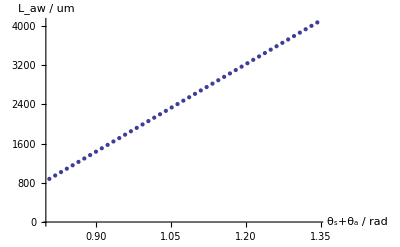

```mathematica
ListPlot[alllengths,AxesLabel->{"θ_s+θ_a / rad","L_aw / um"}]
```

```mathematica
allrs=Table[{angles⟦j⟧,Rn angles⟦j⟧},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

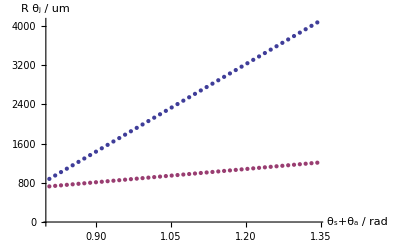

```mathematica
ListPlot[{alllengths,allrs},AxesLabel->{"θ_s+θ_a / rad","R θ_j / um"}](* Plot Subscript[L, j], Subscript[R, j] together *)
```

```mathematica
(*Table[{alllengths⟦j,1⟧,alllengths⟦j,2⟧-alllengths⟦j-1,2⟧},{j,2,nn,1}]*)(* Check that Lj+1 - Lj = dL / 2 *)
```

```mathematica
sumqs=Table[{angles⟦j⟧,alllengths⟦j,2⟧-allrs⟦j,2⟧},{j,1,nn,1}];(* S + Q = L - R θ *)
```

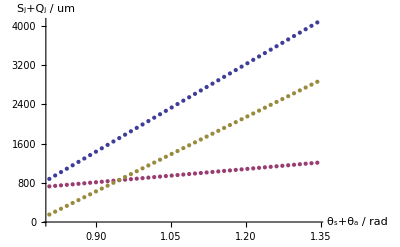

```mathematica
ListPlot[{alllengths,allrs,sumqs},AxesLabel->{"θ_s+θ_a / rad","S_j+Q_j / um"}](* Plot Subscript[L, j], Subscript[R, j] together *)
```

```mathematica
allss=Table[{angles⟦j⟧,(Ls/2-alllengths⟦j,2⟧-Lf Cos[angles⟦j⟧]+allrs⟦j,2⟧-Rn Sin[angles⟦j⟧])/(Cos[angles⟦j⟧]-1)},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

```mathematica
(* Check to see that all Subscript[S, j] are positive *)
j=1;
While[j≤ nn,
If[allss⟦j,2⟧<0.0,Print["j = ",j,": Rj < 0"];Break[];];
j++
]
```

j = 1: Rj < 0

```mathematica
(* There's some condition on the value of R that ensures that Sj < Lj *)
(* This will also affect Subscript[Q, j] *)
(* Should try and find what that is *)
```

```mathematica
allss⟦1⟧
```

{0.807044,-59.583}

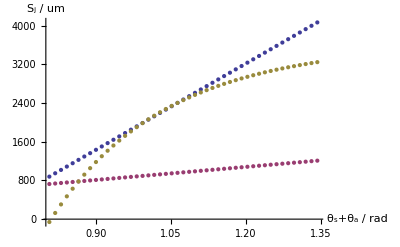

```mathematica
ListPlot[{alllengths,allrs,allss},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}](* Plot Subscript[L, j], Subscript[S, j] together *)
```

```mathematica
(* Try and find the value of θ for which the curve allss is maximum *)
(*allderss=Table[{angles⟦j⟧,(2 Rn (Cos[angles⟦j⟧]-1)+(Ls/2-Lf-alllengths⟦j,2⟧+Rn angles⟦j⟧)Sin[angles⟦j⟧])/(Cos[angles⟦j⟧]-1)^2},{j,1,nn,1}]; *)(* Compute the lengths of all straight connecting sections *)
```

```mathematica
(*ListPlot[{alllengths,allrs,allss,allderss},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]*)(* Plot Subscript[L, j], Subscript[S, j] together *)
```

```mathematica
(* Try and find the value of θ for which the curve allss is maximum *)
(*all2derss=Table[{angles⟦j⟧,1/4(Csc[angles⟦j⟧])^4((Lf+alllengths⟦j,2⟧-Ls/2-Rn angles⟦j⟧)(2+Cos[angles⟦j⟧])+3 Rn Sin[angles⟦j⟧])},{j,1,nn,1}]; *)(* Compute the lengths of all straight connecting sections *)
```

```mathematica
(*ListPlot[{allss,allderss,all2derss},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]*)(* Plot Subscript[L, j], Subscript[S, j] together *)
```

```mathematica
allqs=Table[{angles⟦j⟧,alllengths⟦j,2⟧-allss⟦j,2⟧-allrs⟦j,2⟧},{j,1,nn,1}];
(*allqs=Table[{angles⟦j⟧,Qn},{j,1,nn,1}]; *)
(* Compute the lengths of all straight connecting sections *)
```

```mathematica
(* Check to see that all Subscript[S, j] are positive *)
j=1;
While[j≤ nn,
If[allqs⟦j,2⟧<0.0,Print["j = ",j,": Qj < 0"];Break[];];
j++
]
```

j = 2: Qj < 0

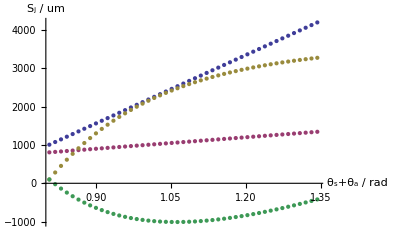

```mathematica
ListPlot[{alllengths,allrs,allss,allqs},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}](* Plot Subscript[L, j], Subscript[S, j], Subscript[Q, j] together *)
```

```mathematica
alltotalL=Table[{angles⟦j⟧,(allss⟦j,2⟧+allqs⟦j,2⟧+allrs⟦j,2⟧)},{j,1,nn,1}];(* Compute total length using Subscript[S, j], Subscript[Q, j], Subscript[R, j] *)
```

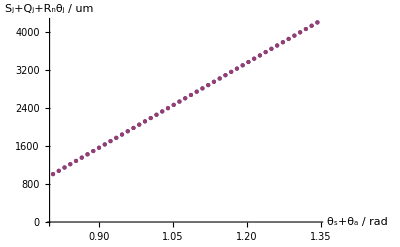

```mathematica
ListPlot[{alltotalL,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j+Q_j+R_nθ_j / um"}](* Plot lengths computed by the two methods *)
```

```mathematica
alldiffl=Table[{angles⟦j⟧,alllengths⟦j,2⟧-alltotalL⟦j,2⟧},{j,1,nn,1}];
```

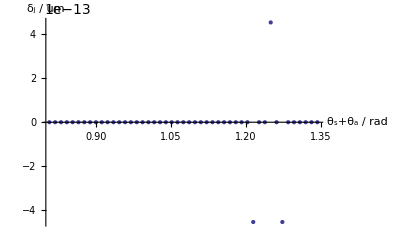

```mathematica
ListPlot[alldiffl,AxesLabel->{"θ_s+θ_a / rad","δ_j / um"}]
```

```mathematica
(* Is the separation constraint satisfied in all cases? *)
allLs=Table[{angles⟦j⟧,(Lf+allss⟦j,2⟧)Cos[angles⟦j⟧]+Rn Sin[angles⟦j⟧]+allqs⟦j,2⟧},{j,1,nn,1}]
```

{{0.807044,1484.57},{0.818704,1484.57},{0.830364,1484.57},{0.842024,1484.57},{0.853684,1484.57},{0.865344,1484.57},{0.877004,1484.57},{0.888664,1484.57},{0.900324,1484.57},{0.911984,1484.57},{0.923644,1484.57},{0.935304,1484.57},{0.946964,1484.57},{0.958624,1484.57},{0.970284,1484.57},{0.981944,1484.57},{0.993604,1484.57},{1.00526,1484.57},{1.01692,1484.57},{1.02858,1484.57},{1.04024,1484.57},{1.0519,1484.57},{1.06356,1484.57},{1.07522,1484.57},{1.08688,1484.57},{1.09854,1484.57},{1.1102,1484.57},{1.12186,1484.57},{1.13352,1484.57},{1.14518,1484.57},{1.15684,1484.57},{1.1685,1484.57},{1.18016,1484.57},{1.19182,1484.57},{1.20348,1484.57},{1.21514,1484.57},{1.2268,1484.57},{1.23846,1484.57},{1.25012,1484.57},{1.26178,1484.57},{1.27344,1484.57},{1.2851,1484.57},{1.29676,1484.57},{1.30842,1484.57},{1.32008,1484.57},{1.33174,1484.57},{1.3434,1484.57}}

```mathematica
Ls/2
```

1484.57

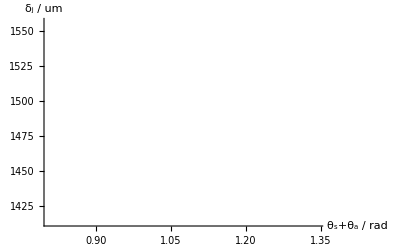

```mathematica
ListPlot[allLs,AxesLabel->{"θ_s+θ_a / rad","δ_j / um"}]
```

## Length of all arrayed waveguides given Rmin, Smin and θmin - Type II Layout Alt

```mathematica
T1=-0.268184; (* Angle that first array waveguide makes with horizontal *)
dT = Abs[0.268184 - 0.256524]; (* angle separation between array waveguides on input/output aperture *)
Lf=857.62; (* length of slab region *)
Sn=100; (* min. length of array straight section *)
Qn=1000; (* min. length of middle straight section *)
Rn=1000;(* smallest array bend radius *)
dL=138.63; (* Array optical path-length difference *)
nn=47; (* Number of arrayed Waveguides *)
```

```mathematica
SepII[Rn_,Ta_,Ti_,Lf_,Sn_,Qn_]:=2(Rn Sin[Ti+Ta]+(Lf+Sn)Cos[Ti+Ta]+Qn); (* separation between slab regions *)
```

```mathematica
LtjII[Qn_,Sn_,Rn_,Ti_,Ta_,dL_,j_]:=Sn+Qn+Rn (Ti+Ta)+(j-1)dL/2;(* Known length of jth arm of arrayed waveguide *)
```

```mathematica
(* Test to see if the numerical and analytical formulae give the same answer for slab separation *)
data=FindMaximum[SepII[Rn,x,T1,Lf,Sn,Qn],{x,(70π)/180}];(* Find angle Ta which maximises slab separation *)
Ta=ArcTan[Rn/(Lf+Sn)]-T1; (* Exact value of angle Ta which maximises slab separation *)
Ls=SepII[Rn,Ta,T1,Lf,Sn,Qn]; (* Computed slab separation *)

Print["Numerical Ta-deg = ",(180data⟦2,-1,-1⟧)/π,", Ta-rad = ",data⟦2,-1,-1⟧,", Analytical θ^a = θ_n^max - θ_i^s = ",Ta," rad"]
Print["Numerical 1/2Ls = ",data⟦1⟧/2," um, Analytical 1/2Ls = ",Ls/2," um"]
Print["Min Length: Sn + Rn (T1 + Ta) = ",Sn+Qn+Rn (T1+Ta)]
```

Numerical Ta-deg = 61.606, Ta-rad = 1.07523, Analytical θ^a = θ_n^max - θ_i^s = 1.07523 rad

Numerical 1/2Ls = 2384.57 um, Analytical 1/2Ls = 2384.57 um

Min Length: Sn + Rn (T1 + Ta) = 1907.04

```mathematica
angles=Table[Ta+T1+(j-1)dT,{j,1,nn,1}];
```

```mathematica
alllengths = Table[{angles⟦j⟧,LtjII[Qn,Sn,Rn,T1,Ta,dL,j]},{j,1,nn,1}]; (* Compute all known lengths of the AWG arms *)
```

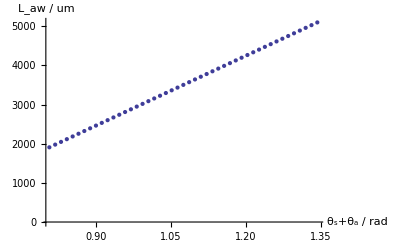

```mathematica
ListPlot[alllengths,AxesLabel->{"θ_s+θ_a / rad","L_aw / um"}]
```

```mathematica
allrs=Table[{angles⟦j⟧,Rn(Ta+T1+(j-1)dT)},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

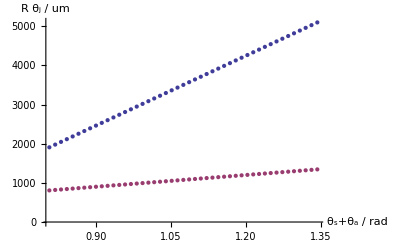

```mathematica
ListPlot[{alllengths,allrs},AxesLabel->{"θ_s+θ_a / rad","R θ_j / um"}](* Plot Subscript[L, j], Subscript[R, j] together *)
```

```mathematica
allqs=Table[{angles⟦j⟧,(Rn Sin[angles⟦j⟧]+(Lf+alllengths⟦j,2⟧-Rn angles⟦j⟧)Cos[angles⟦j⟧]-Ls/2)/(Cos[angles⟦j⟧]-1)},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

```mathematica
(* Check to see that all Subscript[S, j] are positive *)
j=1;
While[j≤ nn,
If[allqs⟦j,2⟧<0.0,Print["j = ",j,": Rj < 0"];Break[];];
j++
]
```

j = 15: Rj < 0

```mathematica
Min[allqs]
```

-110.063

```mathematica
res=MinWithIndx[allqs]
```

Min. pos: 1.06356, Min. val: -110.063

{23,1.06356,-110.063}

```mathematica
res⟦2⟧180/π
```

60.9377

```mathematica
angles⟦1⟧180/π+(angles⟦-1⟧180/π-angles⟦1⟧180/π)/2
```

61.6058

```mathematica
(angles⟦-1⟧180/π-angles⟦1⟧180/π)/2
```

15.3656

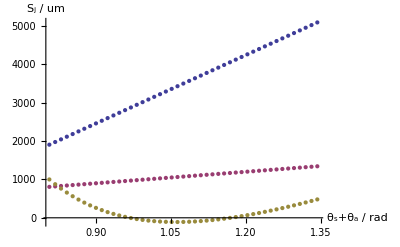

```mathematica
ListPlot[{alllengths,allrs,allqs},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}](* Plot Subscript[L, j], Subscript[S, j] together *)
```

```mathematica
(* There's some condition on the value of R that ensures that Sj < Lj *)
(* This will also affect Subscript[Q, j] *)
(* Should try and find what that is *)
```

```mathematica
(*derqs=Table[{angles⟦j⟧,(Sin[angles⟦j⟧](Lf+alllengths⟦j,2⟧-Ls/2-Rn angles⟦j⟧+Rn Sin[angles⟦j⟧]))/(Cos[angles⟦j⟧]-1)^2},{j,1,nn,1}]; *)(* Compute the lengths of all straight connecting sections *)
```

```mathematica
(*subderqs=Table[{angles⟦j⟧,(Lf+alllengths⟦j,2⟧-Ls/2-Rn angles⟦j⟧+Rn Sin[angles⟦j⟧])},{j,1,nn,1}];*)
```

```mathematica
(*ListPlot[{allqs,derqs,subderqs},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}]*)(* Plot Subscript[L, j], Subscript[S, j] together *)
```

```mathematica
allss=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-allqs⟦j,2⟧-allrs⟦j,2⟧},{j,1,nn,1}]; (* Compute the lengths of all straight connecting sections *)
```

```mathematica
(* Check to see that all Subscript[S, j] are positive *)
j=1;
While[j≤ nn,
If[allss⟦j,2⟧<0.0,Print["j = ",j,": Qj < 0"];Break[];];
j++
]
```

```mathematica
allss⟦1⟧
```

{0.807044,100.}

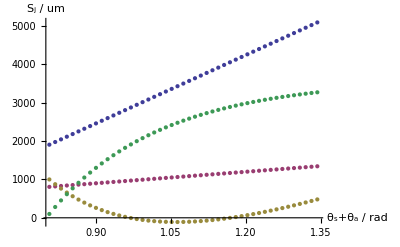

```mathematica
ListPlot[{alllengths,allrs,allqs,allss},AxesLabel->{"θ_s+θ_a / rad","S_j / um"}](* Plot Subscript[L, j], Subscript[S, j], Subscript[Q, j] together *)
```

```mathematica
alltotalL=Table[{Ta+T1+(j-1)dT,(allss⟦j,2⟧+allqs⟦j,2⟧+Rn(Ta+T1+(j-1)dT))},{j,1,nn,1}];(* Compute total length using Subscript[S, j], Subscript[Q, j], Subscript[R, j] *)
```

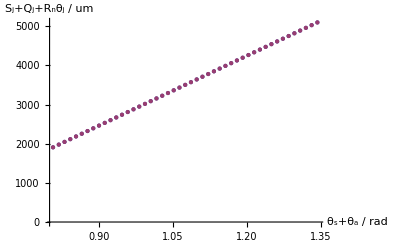

```mathematica
ListPlot[{alltotalL,alllengths},AxesLabel->{"θ_s+θ_a / rad","S_j+Q_j+R_nθ_j / um"}](* Plot lengths computed by the two methods *)
```

```mathematica
alldiffl=Table[{Ta+T1+(j-1)dT,alllengths⟦j,2⟧-alltotalL⟦j,2⟧},{j,1,nn,1}];
```

```mathematica
alldiffl⟦15⟧
```

{0.970284,0.}

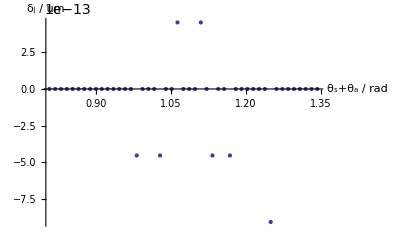

```mathematica
ListPlot[alldiffl,AxesLabel->{"θ_s+θ_a / rad","δ_j / um"}]
```

## S-Bend Geometry

```mathematica
(* Need to figure out the best way to construct the s-bend *)
```

```mathematica
ChordLength[r_, a_]:=2 r Sin[a/2];
```

```mathematica
distance[x1_,y1_, x2_,y2_]:=√((x2-x1)^2+(y2-y1)^2);
```

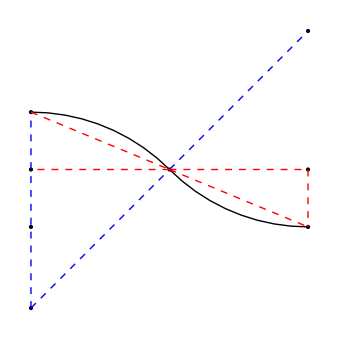

```mathematica
x1=0; y1=0;
R1=17.9382;
θ1=π/4;θ2=π/2;
θ3=π+θ1;θ4=θ3+θ1;
x2 = 2 R1 Cos[θ1];y2 = 2 R1 Sin[θ1];
aa={x1,R1}; gg={x1,R1 Sin[θ1]}; ff={R1 Cos[θ1],R1 Sin[θ1]}; hh={x2,R1 Sin[θ1]}; ee={x2,R1(2Sin[θ1]-1)}; bb={x1,R1(2Sin[θ1]-1)};
Graphics[
{
{PointSize[Large],Point[{x1,y1}],Point[aa],Point[ff],Point[gg],Point[{x2,y2}],Point[hh],Point[ee],Point[bb]},
{Thick,Circle[{x1,y1},R1,{θ1,θ2}],Circle[{x2,y2},R1,{θ3,θ4}]},
{Dashed,Blue,
Line[{{x1,y1},aa}],Line[{{x1,y1},ff}],Line[{ff,{x2,y2}}],Line[{{x2,y2},{x2,y2}}],
Red,
Line[{aa,ff}],Line[{ff,gg}],Line[{ff,hh}],Line[{hh,ee}],Line[{ff,ee}]
}
},AspectRatio->1
]
```

```mathematica
Print["Chord Length C1: ",ChordLength[R1, θ2-θ1]]
Print["Chord Length C1: ",N[ChordLength[R1, θ2-θ1]]," = Euclidean Distance: ",N[distance[aa⟦1⟧,aa⟦2⟧, ff⟦1⟧,ff⟦2⟧]]]
Print["Chord Length C1: ",N[ChordLength[R1, θ2-θ1]]," = Euclidean Distance: ",N[√((distance[aa⟦1⟧,aa⟦2⟧, gg⟦1⟧,gg⟦2⟧])^2+(distance[ff⟦1⟧,ff⟦2⟧, gg⟦1⟧,gg⟦2⟧])^2)]]
```

Chord Length C1: 13.7293

Chord Length C1: 13.7293 = Euclidean Distance: 13.7293

Chord Length C1: 13.7293 = Euclidean Distance: 13.7293

```mathematica
Print["Chord Length C1+C2: ",ChordLength[R1, θ2-θ1]+ChordLength[R1, θ4-θ3]]
Print["Chord Length C1: ",N[ChordLength[R1, θ2-θ1]+ChordLength[R1, θ4-θ3]]," = Euclidean Distance: ",N[distance[aa⟦1⟧,aa⟦2⟧, ee⟦1⟧,ee⟦2⟧]]]
Print["Chord Length C1: ",N[ChordLength[R1, θ2-θ1]+ChordLength[R1, θ4-θ3]]," = Euclidean Distance: ",N[√((distance[aa⟦1⟧,aa⟦2⟧, bb⟦1⟧,bb⟦2⟧])^2+(distance[bb⟦1⟧,bb⟦2⟧, ee⟦1⟧,ee⟦2⟧])^2)]]
```

Chord Length C1+C2: 27.4586

Chord Length C1: 27.4586 = Euclidean Distance: 27.4586

Chord Length C1: 27.4586 = Euclidean Distance: 27.4586

```mathematica
Print["R: ",1/4 Csc[π/8] √((distance[aa⟦1⟧,aa⟦2⟧, bb⟦1⟧,bb⟦2⟧])^2+(distance[bb⟦1⟧,bb⟦2⟧, ee⟦1⟧,ee⟦2⟧])^2)]
```

R: 17.9382

```mathematica
Print["R: ",N[1/4 Csc[π/8] √((distance[aa⟦1⟧,aa⟦2⟧, bb⟦1⟧,bb⟦2⟧])^2+(distance[bb⟦1⟧,bb⟦2⟧, ee⟦1⟧,ee⟦2⟧])^2)]]
```

R: 17.9382

```mathematica
Print["dX: ",N[√((distance[bb⟦1⟧,bb⟦2⟧, ee⟦1⟧,ee⟦2⟧])^2)]];
Print["dY: ",N[√((distance[aa⟦1⟧,aa⟦2⟧,bb⟦1⟧,bb⟦2⟧])^2)]];
Print["ds: ",N[√((distance[aa⟦1⟧,aa⟦2⟧,ee⟦1⟧,ee⟦2⟧])^2)]];
```

dX: 25.3684

dY: 10.508

ds: 27.4586

```mathematica
Print["dX: ",N[√((distance[bb⟦1⟧,bb⟦2⟧, ff⟦1⟧,ff⟦2⟧])^2)]];
Print["dY: ",N[√((distance[aa⟦1⟧,aa⟦2⟧,gg⟦1⟧,gg⟦2⟧])^2)]];
Print["ds: ",N[√((distance[aa⟦1⟧,aa⟦2⟧,gg⟦1⟧,gg⟦2⟧])^2)]];
Print["Tan[α]: ",N[(√((distance[aa⟦1⟧,aa⟦2⟧,gg⟦1⟧,gg⟦2⟧])^2))/(√((distance[bb⟦1⟧,bb⟦2⟧, ff⟦1⟧,ff⟦2⟧])^2))]];
Print["α: ",N[ArcTan[(√((distance[aa⟦1⟧,aa⟦2⟧,gg⟦1⟧,gg⟦2⟧])^2))/(√((distance[bb⟦1⟧,bb⟦2⟧, ff⟦1⟧,ff⟦2⟧])^2))] 180/π]," deg"];
```

dX: 13.7293

dY: 5.25398

ds: 5.25398

Tan[α]: 0.382683

α: 20.941 deg

```mathematica
Tan[π/6]
```

1/(√3)

## S-Bend Geometry

```mathematica
(* Try and get the diagram based on knowing the value of dX and dY only *)
```

```mathematica
ChordRadius[c_,a_]:=c/2 Csc[a/2];
```

```mathematica
dX = 10; 
dY = 10; 
dS = √(dX^2+dY^2);
θ1=π/4;
θ2=θ1+π/4;
R = ChordRadius[dS, θ1];
x1=0;x2=x1+dX; 
y1=R;  y2=y1-dY; 
aa={x1,y1};gg={x1,y2};ff={x2,y2};
```

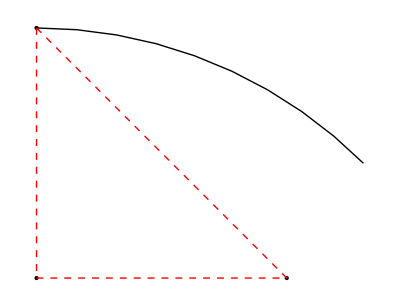

```mathematica
Graphics[
{
{PointSize[Large],Point[aa],Point[gg],Point[ff]},
{Thick, Circle[{x1,0},R,{θ1,θ2}]},
{Dashed, Red,Line[{aa,gg,ff,aa}]}
}]
```

## Scratchpad

```mathematica
D[Cos[x]-1,x]
```

-Sin[x]

```mathematica
D[1-Cos[x],x]
```

Sin[x]

```mathematica
D[x Cos[x]-Sin[x],x]
```

-x Sin[x]

```mathematica
D[f[x]/g[x],x]
```

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

```mathematica
ff=D[(aa-bb Cos[x]+rr (x Cos[x]-Sin[x]))/(1-Cos[x]),x]
```

-((aa-bb Cos[x]+rr (x Cos[x]-Sin[x])) Sin[x])/(1-Cos[x])^2+(bb Sin[x]-rr x Sin[x])/(1-Cos[x])

```mathematica
Solve[ff==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-((aa-bb Cos[x]+rr (x Cos[x]-Sin[x])) Sin[x])/(1-Cos[x])^2+(bb Sin[x]-rr x Sin[x])/(1-Cos[x])==0,x]

```mathematica
FullSimplify[ff]
```

1/4 Csc[x/2]^4 Sin[x] (-aa+bb-rr x+rr Sin[x])

```mathematica
Solve[-aa+bb-rr x+rr Sin[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-aa+bb-rr x+rr Sin[x]==0,x]

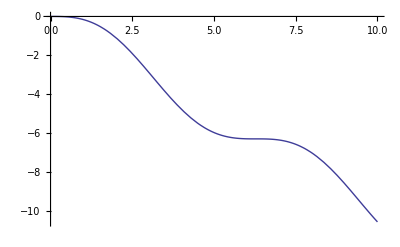

```mathematica
Plot[Sin[x]-x,{x,0,10}]
```

```mathematica
Simplify[1/Sin[x]]
```

Csc[x]

```mathematica
Sin[2π]
```

0

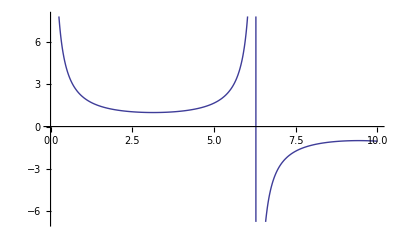

```mathematica
Plot[Csc[x/2],{x,0,10}]
```

### Differentiate Sj

```mathematica
Clear[Lf,Ls]
```

```mathematica
(* Ensure that you solved the equations correctly *)
```

```mathematica
Sres=Solve[(Lf+S)Cos[θ]+(Lj-R θ -S)+R Sin[θ]==Ls/2,S]⟦1,-1,-1⟧
```

(-2 Lj+Ls+2 R θ-2 Lf Cos[θ]-2 R Sin[θ])/(2 (-1+Cos[θ]))

```mathematica
FullSimplify[Sres]
```

(-2 Lj+Ls+2 R θ-2 Lf Cos[θ]-2 R Sin[θ])/(-2+2 Cos[θ])

```mathematica
(* Differentiate Sj *)
```

```mathematica
dSres=D[Sres,θ]
```

(2 R-2 R Cos[θ]+2 Lf Sin[θ])/(2 (-1+Cos[θ]))+(Sin[θ] (-2 Lj+Ls+2 R θ-2 Lf Cos[θ]-2 R Sin[θ]))/(2 (-1+Cos[θ])^2)

```mathematica
FullSimplify[dSres]
```

(-4 R+4 R Cos[θ]+(-2 Lf-2 Lj+Ls+2 R θ) Sin[θ])/(2 (-1+Cos[θ])^2)

```mathematica
(*Compute Second Derivative Sj *)
```

```mathematica
ddSres=D[Sres,{θ,2}]
```

(Sin[θ] (2 R-2 R Cos[θ]+2 Lf Sin[θ]))/(-1+Cos[θ])^2+(2 Lf Cos[θ]+2 R Sin[θ])/(2 (-1+Cos[θ]))+1/2 (-2 Lj+Ls+2 R θ-2 Lf Cos[θ]-2 R Sin[θ]) (Cos[θ]/(-1+Cos[θ])^2+(2 Sin[θ]^2)/(-1+Cos[θ])^3)

```mathematica
FullSimplify[ddSres]
```

1/8 Csc[θ/2]^4 ((2 Lf+2 Lj-Ls-2 R θ) (2+Cos[θ])+6 R Sin[θ])

### Differentiate Qj

```mathematica
Clear[Lf,Ls]
```

```mathematica
res=Solve[(Lf+(Lj-R θ -Qj))Cos[θ]+Qj+R Sin[θ]==Ls/2,Qj]⟦1,-1,-1⟧
```

(-Ls+2 Lf Cos[θ]+2 Lj Cos[θ]-2 R θ Cos[θ]+2 R Sin[θ])/(2 (-1+Cos[θ]))

```mathematica
FullSimplify[res]
```

(-Ls+2 (Lf+Lj-R θ) Cos[θ]+2 R Sin[θ])/(2 (-1+Cos[θ]))

```mathematica
FullSimplify[D[res,θ]]
```

(Sin[θ] (2 Lf+2 Lj-Ls-2 R θ+2 R Sin[θ]))/(2 (-1+Cos[θ])^2)

```mathematica
Cos[π+π/3]
```

-1/2

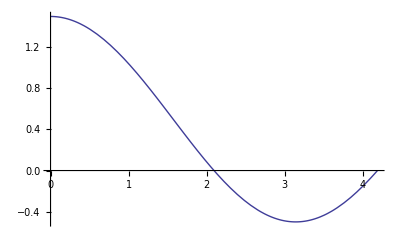

```mathematica
Plot[Cos[θ]+1/2,{θ,0,π+π/3}]
```

```mathematica
FindRoot[Cos[θ]+1/2==0,{θ,2}]
```

{θ→2.0944}

```mathematica
2.0944×180/π
```

120.

```mathematica
90+30
```

120

```mathematica
8/12
```

2/3

```mathematica
(2π)/3 180/π//N
```

120.

```mathematica
Tan[π/4]
```

1

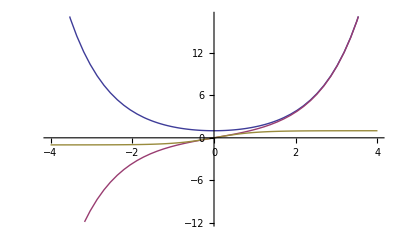

```mathematica
Plot[{Cosh[x],Sinh[x],Tanh[x]},{x,-4,4}]
```

```mathematica
Limit[Tanh[x],x->∞]
```

1

```mathematica
Tan[π/3]
```

√3

```mathematica
TrigExpand[Tan[x+π/2]]
```

-Cot[x]

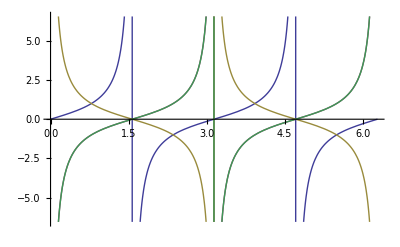

```mathematica
Plot[{Tan[x],Tan[x+π/2],Cot[x],-Cot[x]},{x,0,2π}]
```

```mathematica
N[Tan[1]]
```

1.55741

```mathematica
N[Tan[1+π/2]]
```

-0.642093

```mathematica
N[-Cot[1]]
```

-0.642093